Tan[x] y[x]+y'[x]==Sin[2 x]

{{y→Function[{x},-2 (-2 Cos[x]+Cos[x]^2)]}}

-2 (2 Sin[x]-2 Cos[x] Sin[x])-2 (-2 Cos[x]+Cos[x]^2) Tan[x]==Sin[2 x]

True

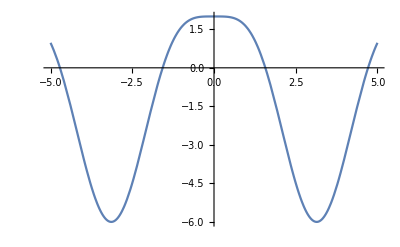

```mathematica
eq = y'[x]+y[x]Tan[x]==Sin[2x]
s0 = DSolve[{eq,y[0]==2},y,x]
(eq)/.s0[[1]]
Simplify[(eq)/.s0[[1]]]
Plot[y[x]/.s0[[1]]/.C[1]->c1,{x, -5, 5}]
```

```mathematica
Evaluate[y[t]/.s0[[1]]/.{C[1]->c1,C[2]->c2}]
```

c1 ⅇ^(1/2 (-b/a-(√(b^2-4 a c))/a) t)+c2 ⅇ^(1/2 (-b/a+(√(b^2-4 a c))/a) t)

```mathematica
y[t]/.DSolve[{eq,y[0]==y0,y'[0]==v0},y,x][[1]]
```

(-2 a ⅇ^(1/2 (-1/a-(√(1-4 a))/a) t) v0+2 a ⅇ^(1/2 (-1/a+(√(1-4 a))/a) t) v0-ⅇ^(1/2 (-1/a-(√(1-4 a))/a) t) y0+√(1-4 a) ⅇ^(1/2 (-1/a-(√(1-4 a))/a) t) y0+ⅇ^(1/2 (-1/a+(√(1-4 a))/a) t) y0+√(1-4 a) ⅇ^(1/2 (-1/a+(√(1-4 a))/a) t) y0)/(2 √(1-4 a))

```mathematica
eq = a*y''[x]+b*y'[x]+c*y[x]==0
s0 = DSolve[eq,y,x]
Simplify[(eq)/.s0[[1]]]
Manipulate[Plot[Evaluate[y[t]/.DSolve[{a*y''[x]+b*y'[x]+c*y[x]==0,y[0]==0,y'[0]==1},y,x][[1]]],{t,-5,5}],
{a,1,5},{b,1,5},{c,1,5}]
```

c y[x]+b y'[x]+a y''[x]==0

{{y→Function[{x},ⅇ^(1/2 (-b/a-(√(b^2-4 a c))/a) x) C[1]+ⅇ^(1/2 (-b/a+(√(b^2-4 a c))/a) x) C[2]]}}

True

```mathematica
eq = {(y'[x])^2+y[x]==a,y[0]==b}
s0 = DSolve[eq,y,x]
Simplify[(eq)/.s0[[1]]]
Manipulate[Plot[Evaluate[y[t]/.DSolve[{(y'[x])^2+y[x]==a,y[0]==b},y,x][[1]]],{t,-5,5}],
{a,1,5},{b,1,5}]
```

{y[x]+y'[x]^2==a,y[0]==b}

{{y→Function[{x},1/4 (4 b-4 √(a-b) x-x^2)]},{y→Function[{x},1/4 (4 b+4 √(a-b) x-x^2)]}}

{True,True}

```mathematica
eq = {y'[x]+(y[x])^2==a,y[0]==b}
s0 = DSolve[eq,y,x]
Simplify[(eq)/.s0[[1]]]
Manipulate[Plot[Evaluate[y[t]/.DSolve[{y'[x]+(y[x])^2==a,y[0]==b},y,x][[1]]],{t,-5,5}],
{a,1,5},{b,0,5}]
```

{y[x]^2+y'[x]==a,y[0]==b}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},√a Tanh[√a x+ArcTanh[b/(√a)]]]}}

{True,True}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.